-Graphics-

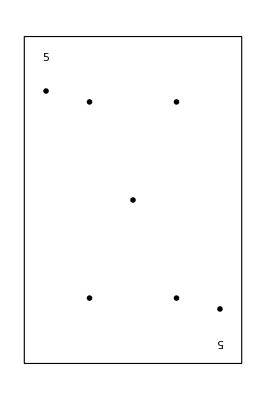
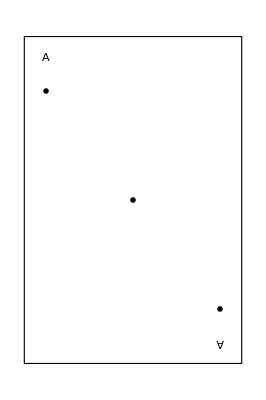
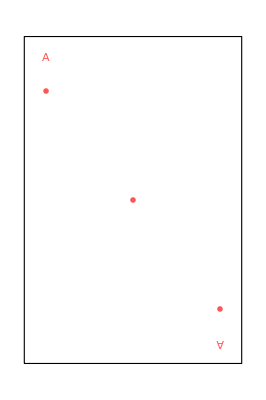
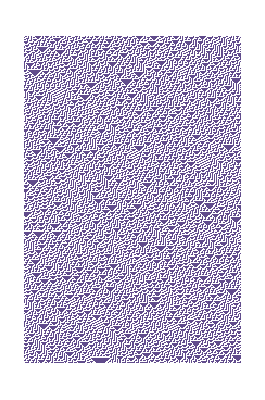
-Graphics--Graphics--Graphics--Graphics--Graphics-

-Graphics-

qual è la probabilità di fare coppia per il giocatore 1?

scegli la probabilita

Inserisci la probabilità che si crei una coppia con: 27 estraendo la prossima carta dal mazzo

Test CalcolaProbabilita

Inserisci la probabilità che si crei una coppia con: 5 estraendo la prossima carta dal mazzo

3/46

Inserisci la probabilità che si crei una coppia con: 6 estraendo la prossima carta dal mazzo

3/46

```mathematica
SetDirectory[NotebookDirectory[]];
Get["randCard.nb"];
Get["calcolaProb.nb"];
player=Input["Inserisci il numero di giocatori: "];
carteScoperte=Input["Inserisci il numero di carte scoperte: "];

(*CREO LE CARTE DEL BANCO E DEL GIOCATORE*)
{carteBanco,carteGiocatore}=randomCards[carteScoperte,player];

(*CREO IL DISEGNO DELLE CARTE AVVERSARIO*)
Switch[player,2,outputavversari=Row[{ImageResize[Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]],carteGiocatore[[4]]}],300]}],3,outputavversari=Row[{ImageResize[ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]],carteGiocatore[[4]]}],300],ImageResize[ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[5]],carteGiocatore[[6]]}],300]}],_,"Errore"];


(*CREO IL DISEGNO DELLE CARTE BANCO*)
outputbanco=Row[{ResourceFunction["PlayingCardGraphic"][carteBanco[[1]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[2]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[3]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[4]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[5]]]},Spacer[10]];
outputbanco;

(*CREO IL DISEGNO DELLE CARTE GIOCATORE*)
outputgiocatore=Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[1]],carteGiocatore[[2]]}];
outputgiocatore;




(*CellPrint[ExpressionCell[Show[table,Graphics[{Inset[outputavversari,{5,4},{Center,Center},{3,4}],Text["10 of Diamonds",{5,3},{Center,Top}]}]],"Output",Background->RGBColor[0.05,0.2,0.1],CellMargins->{{30,30},{10,10}},CellFrame->True,CellFrameColor->RGBColor[0.7,0.2,0.2],CellFrameMargins->5,CellFrameStyle->Thick,CellFrameLabels->{{None,None},{None,"Tavolo da Poker"}},CellLabelPositioning->Left,ShowGroupOpener->False,TextAlignment->Center,FontColor->White,GridBoxBackground->White,GridBoxFrame->"Gridlines",GridBoxFrameStyle->Directive[Thick,White]]];*)


(*DISEGNO LE CARTE*)
If[player>1,Print[outputavversari]]
Print[outputbanco]
Print[outputgiocatore]


Print["qual è la probabilità di fare coppia per il giocatore 1?"]
Print["scegli la probabilita"]
modalita=Input["Inserisci modalità"];
probabilita=calcolaProb[carteBanco,carteGiocatore,player,modalita];

Print[DynamicModule[{valore=0},Column[{Row[{"Inserisci la probabilità: ",InputField[Dynamic[valore],Number,FieldHint->"Inserisci qui il tuo numero"]}],calcolaProb[valore]}]]]

Button["Test CalcolaProbabilita", Print[calcolaProb[{1,2,3,6,0}, {4,5}, 1,1]]]
```

```mathematica
1
```

calcolaProb[{1,2,3,6,0},{4,5},1,1]